Fitting the madgraph partonic cross section to analytical expressions

ALP-only term

Numbers and runcard, param card, proc card all saved in nonresonant_ttbar/partonic_checks/madgraph_cards/ttbar_gg_NR_quad_partonic

```mathematica
mttALP = {575.0,725.0,875.0,1025.0,1175.0,1325.0,1475.0,1625.0,1775.0,1925.0,2075.0,2225.0,2375.0,2525.0,2675.0,2825.0,2975.0,3125.0,3275.0,3425.0,3575.0,3725.0,3875.0,4025.0,4175.0,4325.0,4475.0,4625.0,4775.0,4925.0,5075.0,5225.0,5375.0,5525.0,5675.0,5825.0,5975.0,6125.0,6275.0,6425.0,6575.0,6725.0,6875.0,7025.0,7175.0,7325.0,7475.0,7625.0,7775.0,7925.0,8075.0,8225.0,8375.0,8525.0,8675.0,8825.0,8975.0,9125.0,9275.0,9425.0,9575.0,9725.0,9875.0};
sigmaALP = {4.2864*^-06,4.7215*^-06,4.9242*^-06,5.0544*^-06,5.1326*^-06,5.1743*^-06,5.2157*^-06,5.2422*^-06,5.2609*^-06,5.2855*^-06,5.2837*^-06,5.3125*^-06,5.313*^-06,5.3026*^-06,5.3192*^-06,5.3207*^-06,5.3279*^-06,5.3307*^-06,5.3341*^-06,5.3443*^-06,5.3412*^-06,5.3376*^-06,5.3402*^-06,5.3477*^-06,5.3398*^-06,5.3514*^-06,5.34621*^-06,5.3447*^-06,5.3595*^-06,5.3619*^-06,5.3477*^-06,5.3499*^-06,5.3465*^-06,5.3472*^-06,5.3535*^-06,5.362*^-06,5.3539*^-06,5.3546*^-06,5.3687*^-06,5.36301*^-06,5.3617*^-06,5.3515*^-06,5.3629*^-06,5.3601*^-06,5.3577*^-06,5.3591*^-06,5.3659*^-06,5.3615*^-06,5.3597*^-06,5.3586*^-06,5.3738*^-06,5.355*^-06,5.3576*^-06,5.367*^-06,5.3644*^-06,5.3576*^-06,5.3642*^-06,5.3641*^-06,5.3506*^-06,5.3662*^-06,5.3631*^-06,5.3649*^-06,5.3611*^-06};
```

Recall mtt = √s, i.e. the x-axis is √srather than s itself.
We’d like to fit these numbers to a function of the form

f(x) = Const * ( 1 - (2 m_t^2)/(√s)^2)

```mathematica
mt=172.5 (*GeV*)
Fit[Transpose[{mttALP,sigmaALP}],{1-(2 mt^2)/x^2},x]
```

172.5

5.36266×10^-6 (1-59512.5/x^2)

Plot numbers vs fit function to show agreement:

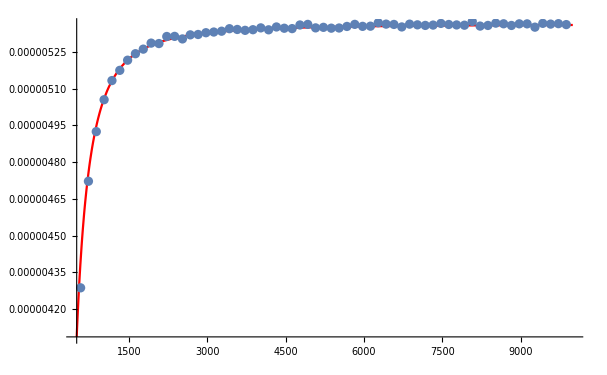

```mathematica
Show[Plot[5.362664775855763*^-6 (1-59512.5/x^2),{x,500,10000},PlotRange->Full,PlotStyle->Red],ListPlot[Transpose[{mttALP,sigmaALP}],PlotRange->Full]]
```

ALP-SM Interference term

Numbers and runcard, param card, proc card all saved in nonresonant_ttbar/partonic_checks/madgraph_cards/ttbar_gg_NR_lin_partonic

```mathematica
mttALPSM = {575.0,725.0,875.0,1025.0,1175.0,1325.0,1475.0,1625.0,1775.0,1925.0,2075.0,2225.0,2375.0,2525.0,2675.0,2825.0,2975.0,3125.0,3275.0,3425.0,3575.0,3725.0,3875.0,4025.0,4175.0,4325.0,4475.0,4625.0,4775.0,4925.0,5075.0,5225.0,5375.0,5525.0,5675.0,5825.0,5975.0,6125.0,6275.0,6425.0,6575.0,6725.0,6875.0,7025.0,7175.0,7325.0,7475.0,7625.0,7775.0,7925.0,8075.0,8225.0,8375.0,8525.0,8675.0,8825.0,8975.0,9125.0,9275.0,9425.0,9575.0,9725.0};
sigmaALPSM = {0.0039034837,0.003015098,0.002352339,0.0018739590000000001,0.0015321199999999999,0.001274303,0.0010763,0.0009206815,0.0007992049,0.0006996131,0.0006186672999999999,0.0005511392,0.0004943339,0.00044586690000000004,0.00040487609999999996,0.0003691594,0.00033814079999999996,0.00031109350000000003,0.0002865586,0.00026592875,0.00024650359,0.00022961453999999998,0.00021456487,0.00020093470000000002,0.00018860081000000002,0.00017726834,0.00016687973000000002,0.00015772052,0.00014936463,0.00014132258000000003,0.00013400463000000002,0.00012719559,0.00012136687,0.00011539718,0.00011018366,0.00010518766800000001,0.00010046122099999998,9.614140800000001*^-05,9.21345*^-05,8.840685099999998*^-05,8.4819435*^-05,8.144388*^-05,7.8269063*^-05,7.5213166*^-05,7.2505596*^-05,6.9920796*^-05,6.752480899999999*^-05,6.5282161*^-05,6.2932061*^-05,6.0834287000000006*^-05,5.881298199999999*^-05,5.6845525000000005*^-05,5.5051548000000004*^-05,5.332111800000001*^-05,5.1747748000000004*^-05,5.0233843000000004*^-05,4.8704618*^-05,4.72306923*^-05,4.58129219*^-05,4.4502341*^-05,4.328053550000001*^-05,4.20319648*^-05};
```

We’d like to fit these numbers to a function of the form

f(x) = Const/s Log(√(s/mt^2))

```mathematica
mt=172.5 (*GeV*);
Fit[Transpose[{mttALPSM,sigmaALPSM}],{1/x^2 Log[x/mt]},x]
```

(1088.01 Log[0.0057971 x])/x^2

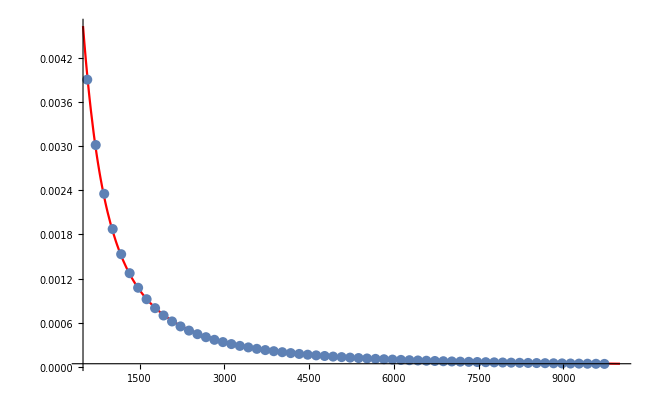

```mathematica
Show[Plot[(1088.0117736073955 Log[0.005797101449275362 x])/x^2,{x,500,10000},PlotRange->Full,PlotStyle->Red],ListPlot[Transpose[{mttALPSM,sigmaALPSM}],PlotRange->Full]]
```

SM gg term

Numbers and runcard, param card, proc card all saved in nonresonant_ttbar/partonic_checks/madgraph_cards/ttbar_gg_NR_SM_partonic

```mathematica
mttSM={575.0,725.0,875.0,1025.0,1175.0,1325.0,1475.0,1625.0,1775.0,1925.0,2075.0,2225.0,2375.0,2525.0,2675.0,2825.0,2975.0,3125.0,3275.0,3425.0,3575.0,3725.0,3875.0,4025.0,4175.0,4325.0,4475.0,4625.0,4775.0,4925.0,5075.0,5225.0,5375.0,5525.0,5675.0,5825.0,5975.0,6125.0,6275.0,6425.0,6575.0,6725.0,6875.0,7025.0,7175.0,7325.0,7475.0,7625.0,7775.0,7925.0,8075.0,8225.0,8375.0,8525.0,8675.0,8825.0,8975.0,9125.0,9275.0,9425.0,9575.0,9725.0};
sigmaSM = {13.8034,11.75109,9.656447,8.003812,6.690689,5.685413,4.8821201,4.2367726,3.7276911999999998,3.2918944,2.9320767,2.6348846999999997,2.380917,2.1592762100000003,1.9699194500000001,1.80958931,1.66278995,1.53181512,1.41975747,1.3201165300000002,1.22878425,1.14895218,1.076632,1.01000997,0.949094817,0.8942208970000001,0.8446403960000001,0.799022353,0.756765048,0.719007269,0.6820824409999999,0.6493976050000001,0.6185630120000001,0.590309614,0.563816287,0.538413589,0.515141307,0.493729318,0.473937359,0.454755659,0.436454032,0.419582647,0.404261752,0.389220703,0.3750697746,0.3615790411,0.3489783853,0.3369976221,0.3256070079,0.3148964845,0.30470596930000005,0.29501552259999997,0.2856551053,0.27695485189999997,0.2684844918,0.2605940926,0.252683786,0.24572360099999999,0.23867338289999998,0.2318731154,0.2254829161,0.2192827196};
```

First we’d like to fit these numbers to a function of the form

f(x) = Const/s Log(√(s/mt^2))

```mathematica
mt=172.5 (*GeV*);
Fit[Transpose[{mttSM,sigmaSM}],{1/x^2 Log[x/mt]},x]
```

(4.32896×10^6 Log[0.0057971 x])/x^2

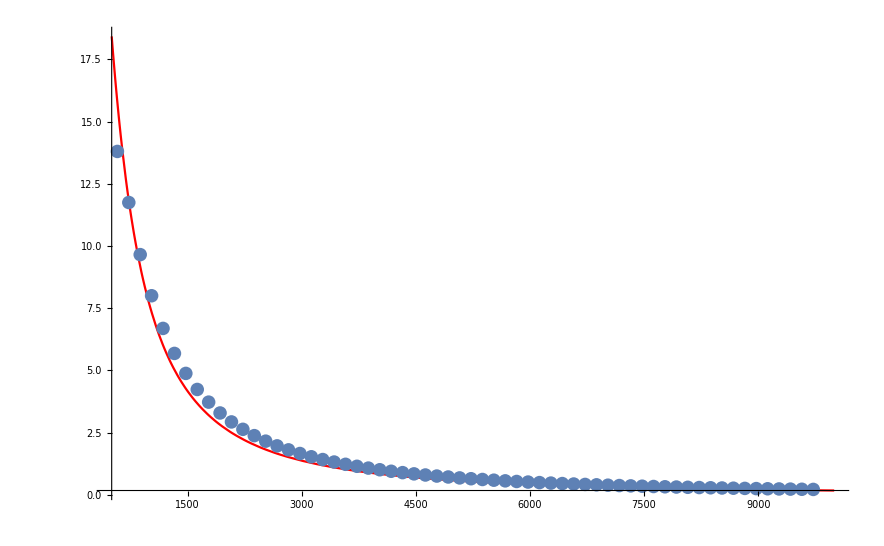

```mathematica
Show[Plot[(4.328960410308754*^6 Log[0.005797101449275362 x])/x^2,{x,500,10000},PlotRange->Full,PlotStyle->Red],ListPlot[Transpose[{mttSM,sigmaSM}],PlotRange->Full]]
```

Second we’d like to fit these numbers to a function of the form

f(x) = const/s(-7+8sLog(√(s/mt^2)))

```mathematica
mt=172.5 (*GeV*);
Fit[Transpose[{mttSM,sigmaSM}],{1/x^2(-7+8Log[x/mt])},x]
```

(1.22537×10^6 (-7+8 Log[0.0057971 x]))/x^2

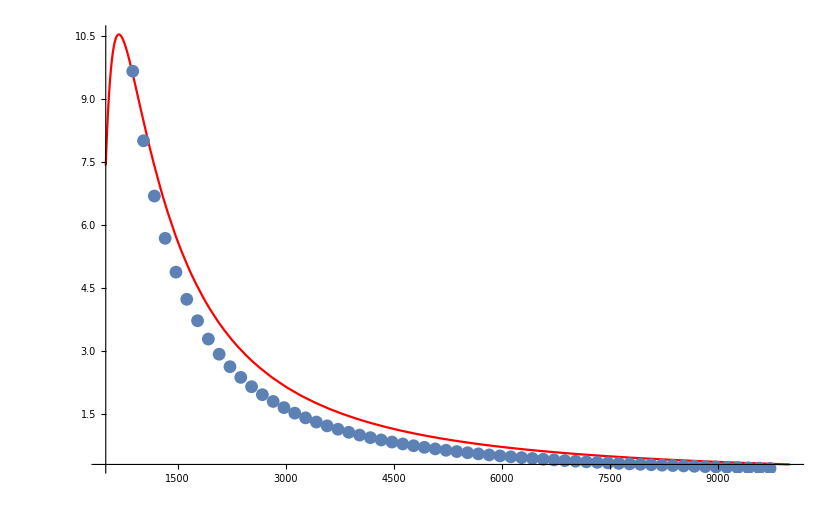

```mathematica
Show[Plot[(1.225366821936036*^6 (-7+8 Log[0.005797101449275362 x]))/x^2,{x,500,10000},PlotRange->Full,PlotStyle->Red],ListPlot[Transpose[{mttSM,sigmaSM}],PlotRange->Full]]
```

Second we’d like to fit these numbers to a function of the form

f(x) = const/s(-7+8sLog(√(s/mt^2))) + mt^2/s^2(-17+ 32sLog(√(s/mt^2)))

```mathematica
mt=172.5 (*GeV*);
Fit[Transpose[{mttSM,sigmaSM}],{1/x^2(-7+8Log[x/mt])+mt^2/x^4(-17+32Log[x/mt])},x]
```

989753. ((-7+8 Log[0.0057971 x])/x^2+(29756.3 (-17+32 Log[0.0057971 x]))/x^4)

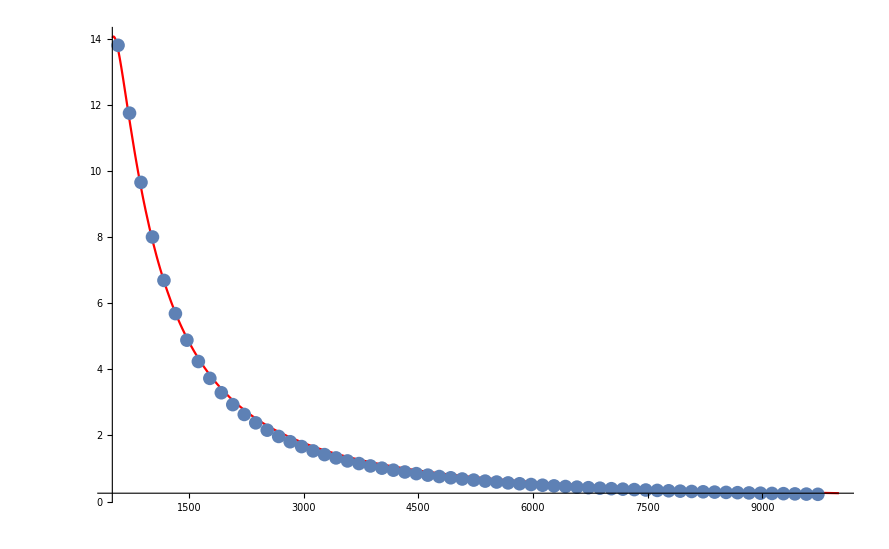

```mathematica
Show[Plot[989753.0207113541 ((-7+8 Log[0.005797101449275362 x])/x^2+(29756.25 (-17+32 Log[0.005797101449275362 x]))/x^4),{x,500,10000},PlotRange->Full,PlotStyle->Red],ListPlot[Transpose[{mttSM,sigmaSM}],PlotRange->Full]]
```